# Task 2 Time complexity

## Functions

## Merge Sort

```mathematica
merge[xIn_,lIn_,mIn_,rIn_]:=Module[
{i,j,k,n1=mIn-lIn,n2=rIn-mIn+1,l,r,arr=xIn,templ=0,tempr=0,result=0,fArr,tempf=0},

l[]=n1;
     r[]=n2;


l=arr[[1;;n1]];
r=arr[[n2;;-1]];

i=1;
j=1;

   For[i = 1, i < Length[l], i++, 
If[l[[i]] > l[[i + 1]],
 {templ = l[[i]];
 l[[i]] = l[[i + 1]];
 l[[i + 1]] = templ; 
i = 0; 
};
 ]; 
]; 

   For[i = 1, i < Length[r], i++, 
If[r[[i]] > r[[i + 1]],
 {tempr = r[[i]];
 r[[i]] = r[[i + 1]];
 r[[i + 1]] = tempr; 
i = 0; 
};
 ]; 
]; 

fArr=Join[l,r];
For[i = 1, i < Length[fArr], i++, 
If[fArr[[i]] > fArr[[i + 1]],
 {tempf = fArr[[i]];
 fArr[[i]] = fArr[[i + 1]];
 fArr[[i + 1]] = tempf; 
i = 0; 
};
 ]; 
]; 

Return@fArr;

]
```

```mathematica
x={5,22,2.13,6,3,8,11,1,7,15,16};
```

```mathematica
merge[x,1,6,11]
```

{1,2.13,3,5,6,7,8,11,15,16,22}

## Quick Sort

```mathematica
Quicksort[array_]:=Module[
{work=array,partitionFun,sortFun},


partitionFun=Function[
{low,high},
Module[

{pivot=work[[high]],
i=low-1,j,tmp},
Do[tmp=work[[j]];
If[tmp≤pivot,i=i+1;
work[[j]]=work[[i]];
work[[i]]=tmp],{j,low,high-1}];
tmp=work[[i+1]];
work[[i+1]]=work[[high]];
work[[high]]=tmp;
i+1]];


sortFun=Function[
{low,high},
If[low<high,
Module[{p=partitionFun[low,high]},
sortFun[low,p-1];
sortFun[p,high]];
1,2]];

sortFun[1,Length[work]];
Return@work
];
```

```mathematica
Quicksort[x]
```

{1,2.13,3,5,6,7,8,11,15,16,22}

## Heap Sort

```mathematica
heapify[array_,N_,I_]:=Module[
{arr=array,n=N,i=I,largest=I,l=2*I+1,r=2*I+2,swap},
If[l<n&& arr[[l]]>arr[[largest]],largest=1;];
If[l<n&& arr[[r]]>arr[[largest]],largest=r;];
If[largest≠ i,
swap=arr[[i]];
arr[[i]]=arr[[largest]];
arr[[largest]]=swap;
heapify[arr,n,largest];
];
];
```

```mathematica
HeappSort[array_]:=Module[
{arr=array,n=Length@array,i=1,temp=0},
i=n/2-1;
i=Round@i;
For[i,i≥ 1,i--,
arr=heapify[arr,n,i];
];

For[i=n-1,i>1,i--,
temp=arr[[1]];
arr[[1]]=arr[[i]];
arr[[i]]=temp;
arr=heapify[arr,i,1];
];
Return@arr;
]
```

```mathematica
HeappSort[x]
```

Part::partd: Part specification Null⟦7⟧ is longer than depth of object.

Part::partd: Part specification Null⟦3⟧ is longer than depth of object.

Part::partd: Part specification Null⟦8⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::partd: Part specification arr$6943⟦1⟧ is longer than depth of object.

Set::partd: Part specification arr$6943⟦i$6943⟧ is longer than depth of object.

Set::partd: Part specification arr$6943⟦1⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

## Measurements

## Data s

```mathematica
dataRandom=Table[RandomInteger[{0,n},n],{n,{10,100,1000,10000,100000}}];
```

```mathematica
dataRandom[[1]]
dataRandom[[2]]
dataAscending=Sort@#&/@dataRandom;
dataAscending[[1]]
dataAscending[[2]]
dataDescending=Reverse@#&/@dataAscending;
dataDescending[[1]]
dataDescending[[2]]
```

{2,10,3,3,10,0,2,2,1,2}

{42,64,77,98,4,83,3,57,26,11,64,87,62,63,74,51,22,2,33,51,77,96,69,88,32,41,58,40,27,35,61,67,20,59,95,1,36,37,27,85,17,36,61,58,68,74,68,22,37,68,74,79,91,60,41,47,68,88,72,62,2,0,45,15,0,27,18,47,14,73,59,91,83,36,8,18,5,97,34,35,90,68,76,65,9,100,7,97,69,70,65,76,42,49,57,40,83,89,9,18}

{0,1,2,2,2,2,3,3,10,10}

{0,0,1,2,2,3,4,5,7,8,9,9,11,14,15,17,18,18,18,20,22,22,26,27,27,27,32,33,34,35,35,36,36,36,37,37,40,40,41,41,42,42,45,47,47,49,51,51,57,57,58,58,59,59,60,61,61,62,62,63,64,64,65,65,67,68,68,68,68,68,69,69,70,72,73,74,74,74,76,76,77,77,79,83,83,83,85,87,88,88,89,90,91,91,95,96,97,97,98,100}

{10,10,3,3,2,2,2,2,1,0}

{100,98,97,97,96,95,91,91,90,89,88,88,87,85,83,83,83,79,77,77,76,76,74,74,74,73,72,70,69,69,68,68,68,68,68,67,65,65,64,64,63,62,62,61,61,60,59,59,58,58,57,57,51,51,49,47,47,45,42,42,41,41,40,40,37,37,36,36,36,35,35,34,33,32,27,27,27,26,22,22,20,18,18,18,17,15,14,11,9,9,8,7,5,4,3,2,2,1,0,0}

## Measuring

### Merge Sort Measuring

```mathematica
measurementMergeSortRandom=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataRandom[[1;;3]]}];
measurementMergeSortAscending=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataAscending[[1;;3]]}];
measurementMergeSortDescending=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataDescending[[1;;3]]}];
```

#### Results

```mathematica
measurementMergeSortRandom
measurementMergeSortAscending
measurementMergeSortDescending
```

{{10,7.09091×10^-7},{100,4.72727×10^-7},{1000,4.63636×10^-7}}

{{10,6.09091×10^-7},{100,5.×10^-7},{1000,5.×10^-7}}

{{10,6.18182×10^-7},{100,3.90909×10^-7},{1000,3.90909×10^-7}}

#### Plots and Graphs

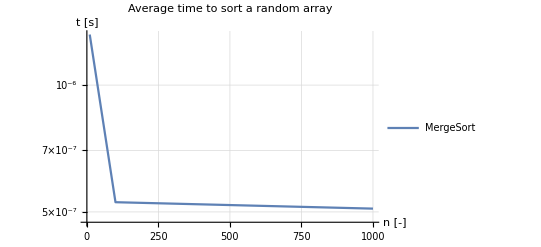

```mathematica
ListLogPlot[measurementMergeSortRandom,
Joined->True,
GridLines->Automatic,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Average time to sort a random array",
PlotLegends->{"MergeSort"}
]
```

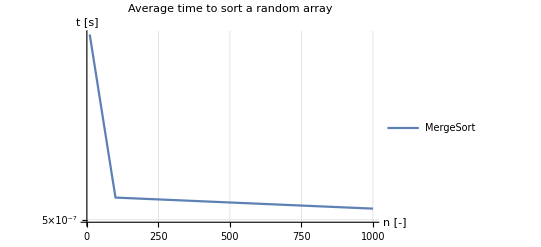

```mathematica
ListLogPlot[measurementMergeSortAscending,
Joined->True,
GridLines->Automatic,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Average time to sort a random array",
PlotLegends->{"MergeSort"}
]
```

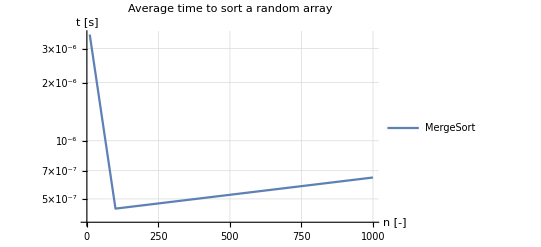

```mathematica
ListLogPlot[measurementMergeSortDescending,
Joined->True,
GridLines->Automatic,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Average time to sort a random array",
PlotLegends->{"MergeSort"}
]
```

#### Bonus Tip

```mathematica
k=measurementMergeSortDescending[[3,2]]/1000^2
t=100000^2*k
t/3600
t=(100000*Log[100000])*k
```

6.45455×10^-13

0.00645455

1.79293×10^-6

7.43107×10^-7

```mathematica
k=measurementMergeSortRandom[[3,2]]/1000^2
t=100000^2*k
t/3600
t=(100000*Log[100000])*k
```

5.09091×10^-13

0.00509091

1.41414×10^-6

5.86113×10^-7

```mathematica
k=measurementMergeSortAscending[[3,2]]/1000^2
t=100000^2*k
t/3600
t=(100000*Log[100000])*k
```

5.09091×10^-13

0.00509091

1.41414×10^-6

5.86113×10^-7

### Quick Sort Measuring

```mathematica
measurementQuickSortRandom=Table[
{Length@d,Mean[Table[AbsoluteTiming[Quicksort@d][[1]],{11}]]}
,{d,dataRandom[[1;;3]]}];
```

```mathematica
measurementQuickSortAscending=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataAscending[[1;;3]]}];
```

```mathematica
measurementQuickSortDescending=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataDescending[[1;;3]]}];
```

#### Results

```mathematica
measurementQuickSortRandom
measurementQuickSortAscending
measurementQuickSortDescending
```

{{10,0.000711882},{100,0.00719427},{1000,0.0688135}}

{{10,7.45455×10^-7},{100,5.09091×10^-7},{1000,5.×10^-7}}

{{10,8.09091×10^-7},{100,5.63636×10^-7},{1000,5.54545×10^-7}}

#### Plots and Graphs

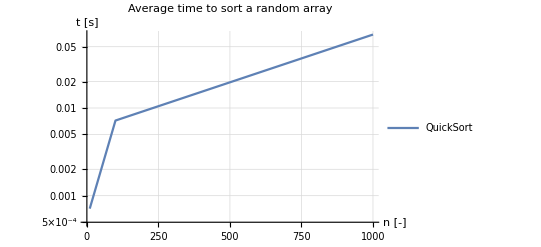

```mathematica
ListLogPlot[measurementQuickSortRandom,
Joined->True,
GridLines->Automatic,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Average time to sort a random array",
PlotLegends->{"QuickSort"}
]
```

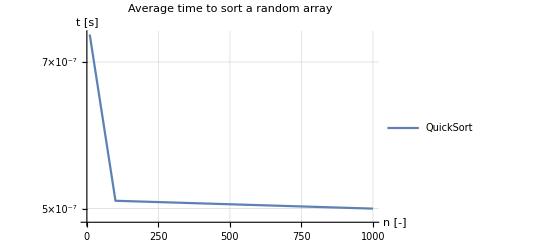

```mathematica
ListLogPlot[measurementQuickSortAscending,
Joined->True,
GridLines->Automatic,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Average time to sort a random array",
PlotLegends->{"QuickSort"}
]
```

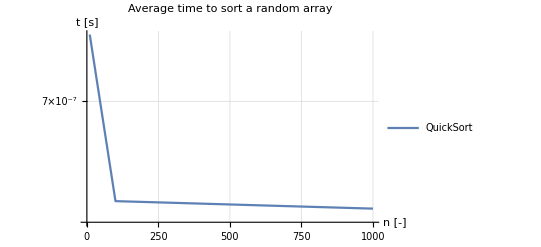

```mathematica
ListLogPlot[measurementQuickSortDescending,
Joined->True,
GridLines->Automatic,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Average time to sort a random array",
PlotLegends->{"QuickSort"}
]
```

#### Bonus Tip

```mathematica
k=measurementQuickSortDescending[[3,2]]/1000^2
t=100000^2*k
t/3600
t=(100000*Log[100000])*k
```

5.54545×10^-13

0.00554545

1.5404×10^-6

6.38444×10^-7

```mathematica
k=measurementQuickSortAscending[[3,2]]/1000^2
t=100000^2*k
t/3600
t=(100000*Log[100000])*k
```

5.×10^-13

0.005

1.38889×10^-6

5.75646×10^-7

```mathematica
k=measurementQuickSortRandom[[3,2]]/1000^2
t=100000^2*k
t/3600
t=(100000*Log[100000])*k
```

6.88135×10^-8

688.135

0.191149

0.0792245

### Heap Sort Measuring

#### // heap sort have some problems

```mathematica
measurementHeapSortRandom=Table[
{Length@d,Mean[Table[AbsoluteTiming[Quicksort@d][[1]],{11}]]}
,{d,dataRandom[[1;;3]]}];
measurementHeapSortAscending=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataAscending[[1;;3]]}];
measurementHeapSortDescending=Table[
{Length@d,Mean[Table[AbsoluteTiming[merge@d][[1]],{11}]]}
,{d,dataDescending[[1;;3]]}];
```

## Conclusion

Sorting algorithms are key to the performance of many important operations like searching, databases ...
There is different levels of sorting. we will explain three different levels of sorting.

First sorting algorithm with complexity of n squared (n^2) .
-Bubble sort 
-Selection Sort 
-Insertion Sort

Second sorting algorithm with complexity of nLOGn (n Log n) .
-Merge Sort
-Quick Sort
-Heap Sort

Third is Hybrid algorithms that combine First and second for best performance. 
-TimSort
-IntroSort

In this task i have implemented all three algorithms of second level with complexity (n Log n) and base on the results and data we can define this algorithms as. 

-Merge sort takes the input list and divides it in half over and over until we are left with a bunch of sub
lists of size 1 that are trivially sorted then the merging process begins merge sort sequentially compares the elements of two sub-lists together to form sorted sub-lists of size 2 size 4 then size a and so on and this happens until it has just one sorted sublist the same size as the input list at this point the list is sorted it takes o of login operations for merge sort to divide an input list of n elements into n sub lists of one element then it takes ov and operations to merge the sublist back together thus merge sort has a time complexity of o of n log n merge sort is also a stable algorithm and it can be further optimized in practice by merging sublists in parallel with one another the big drawback to merge sort is that of auxiliary space is required during the merging process

-quicksort first picks an element from the input list called the pivot then all elements less than the pivot are placed before it and all elements greater than the pivot are placed after it once this step is completed the pivot is in its final position and the input list has been partitioned into two sub lists elements less than the pivot and elements greater than the pivot quicksort then recursively applies the same steps to each sub-list until it has sub-lists of at most one element which is trivially sorted once the recursion is finished the list is sorted on average as long as the chosen pivot divides the input lists into two reasonably sized pieces it takes log n recursive calls to reach a list size of one for each recursive call it takes n operations to place the other elements on the current side of the pivot therefore quicksort has an average time complexity of o of n log n note that the worst case run time of quick sort is actually o of n squared this happens when the chosen pivots are always a minimum or maximum and they actually don’t partition the list at all so this can happen if a bad partition scheme is used on almost sorted data however the probability of this occurring on a large random input is extremely small so we generally consider the worst expected run time of quick sort to be o of n log n in practice quicksort tends to be faster than merge sort and this is because it uses log n stack space as it is recursively partitioning the input list and is usually not implemented as a stable sorting algorithm

-heap sort divides the input list into two parts one sorted and one unsorted initially the sorted section is empty and the unsorted section is the entire input list which is maintained as a heap sort the largest element is extracted from the unsorted heap sector and placed at the start of the sorted section in a constant time operation the unsorted section is then rearranged to maintain its heap and variance this process is repeated until the sorted section is actually the size of the entire list at this point you might have noticed that heap sort sounds strikingly similar to selection sort this is because heapsort is in essence the same but crucially heapsort maintains the unsorted section as a heap hence its name for each iteration instead of scanning through the unsorted section in linear time heapsort can extract its next element in constant time it then can rearrange the elements of the unsorted section to reform a heap in o of log n time this yields an overall run time of o of n log n however since the constant factor behind heap source runtime is larger than that of quicksort it runs slower heapsort’s advantage over the other algorithms in this category is that it doesn’t require any extra space on the other hand though heapsort is not a stable sorting algorithm and this is because of its arbitrary rearrangements of elements to maintain the heap during the sorting process